#### 制作英语常用单词列表的首字母的WordCloud

获取英语常用词列表：

```mathematica
WordList[]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,39160,zoom,zoophyte,zounds,zucchini,zwieback,zydeco,zygote,zygotic}
 |  |  |  |

计算每个单词的长度：

```mathematica
StringLength[WordList[]]
```

{1,3,8,5,6,5,7,7,9,11,5,9,5,7,9,5,9,8,4,6,5,5,10,11,12,8,10,7,9,6,9,9,8,5,4,8,39104,4,6,6,5,7,4,9,4,6,6,3,6,5,6,9,3,6,5,6,8,6,5,4,6,3,10,9,7,4,8,6,8,8,6,6,7}
 |  |  |  |

制作单词长度的直方图：

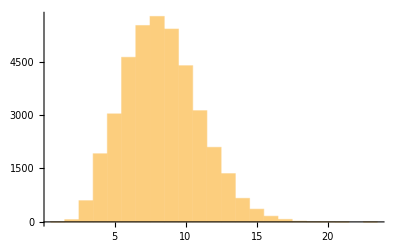

```mathematica
Histogram[StringLength[WordList[]]]
```

获取每个单词的首字母：

```mathematica
StringTake[WordList[],1]
```

{a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,39139,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z}
 |  |  |  |

从首字母列表中制作词云：

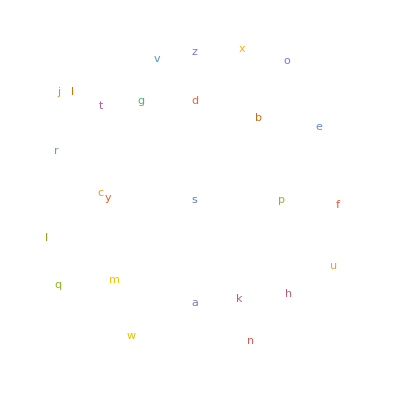

```mathematica
WordCloud[StringTake[WordList[],1]]
```